```mathematica
(* Run to install FeynCalc 
<<FeynCalc`*)
```

```mathematica
Clear["Global`*"]
```

# Construct

## Do Wick’s contractions

```mathematica
(* Define the vertex of the interaction and propagator for the spin-1 massive field *)
Vertex[ω_,k_,mu_,nu_,rho_,sigma_]:=1/2(-(FV[ω,mu]*FV[k,nu]+FV[ω,nu]*FV[k,mu])MT[rho,sigma] + FV[ω,mu]*FV[k,rho]*MT[nu,sigma] + FV[ω,sigma]*FV[k,nu]*MT[mu,rho] + FV[ω,sigma]*FV[k,mu]*MT[nu,rho] +FV[ω,nu]*FV[k,rho]*MT[mu,sigma]-FV[ω,sigma]*FV[k,rho]*MT[mu,nu]+(M^2 + SP[ω,k])*(MT[mu,nu]*MT[rho,sigma] - MT[mu,rho]*MT[nu,sigma] - MT[mu,sigma]*MT[nu,rho]));

Prop[mu_,nu_,k_]:=MT[mu,nu] - (FV[k,mu]*FV[k,nu])/M^2;

(* Rules *)

(* rewrite  et similia *)
Separateql = {
Pair[Momentum[l],Momentum[l]]:>Pair[LorentzIndex[l6],LorentzIndex[l7]]*Pair[LorentzIndex[l6],Momentum[l]]*Pair[LorentzIndex[l7],Momentum[l]],

Pair[Momentum[l],Momentum[q*x]]:>Pair[LorentzIndex[l1],LorentzIndex[q1]]*Pair[LorentzIndex[l1],Momentum[l]]*x*Pair[LorentzIndex[q1],Momentum[q]],
Pair[Momentum[x*q],Momentum[l]]:>Pair[LorentzIndex[q2],LorentzIndex[l2]]*Pair[LorentzIndex[l2],Momentum[l]]*x*Pair[LorentzIndex[q2],Momentum[q]],

Pair[Momentum[q],Momentum[l]]:>Pair[LorentzIndex[q3],LorentzIndex[l3]]*Pair[LorentzIndex[l3],Momentum[l]]*Pair[LorentzIndex[q3],Momentum[q]],
Pair[Momentum[l],Momentum[q]]:>Pair[LorentzIndex[l4],LorentzIndex[q4]]*Pair[LorentzIndex[l4],Momentum[l]]*Pair[LorentzIndex[q4],Momentum[q]]
};

ruleqx = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[x*q]]:>x*Pair[LorentzIndex[a],Momentum[q]],
Pair[LorentzIndex[a_],Momentum[q*x]]:>x*Pair[LorentzIndex[a],Momentum[q]],

(* separate  *)
Pair[Momentum[x*q],Momentum[x*q]]:>x^2 Pair[Momentum[q],Momentum[q]],
Pair[Momentum[x*q],Momentum[q]]:>x*Pair[Momentum[q],Momentum[q]],
Pair[Momentum[q],Momentum[x*q]]:>x*Pair[Momentum[q],Momentum[q]]
};

ruleηlq ={
Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[q]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]]* Pair[LorentzIndex[b],Momentum[q]]*Pair[LorentzIndex[l5],LorentzIndex[q5]]* Pair[LorentzIndex[l5],Momentum[l]]* Pair[LorentzIndex[q5],Momentum[q]],

Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[l]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]]* Pair[LorentzIndex[b],Momentum[l]]*Pair[LorentzIndex[l8],LorentzIndex[l9]]* Pair[LorentzIndex[l8],Momentum[l]]* Pair[LorentzIndex[l9],Momentum[l]]
};

ruleϵL = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[ϵ*l]]:>ϵ*Pair[LorentzIndex[a],Momentum[l]],
Pair[LorentzIndex[a_],Momentum[l*ϵ]]:>ϵ*Pair[LorentzIndex[a],Momentum[l]],

(* separate  *)
Pair[Momentum[ϵ*l],Momentum[ϵ*l]]:>ϵ^2 Pair[Momentum[l],Momentum[l]],
Pair[Momentum[ϵ*l],Momentum[l]]:>ϵ*Pair[Momentum[l],Momentum[l]],
Pair[Momentum[l],Momentum[ϵ*l]]:>ϵ*Pair[Momentum[l],Momentum[l]]
};
```

```mathematica
(* Costruct the numerator *)
Vertex1= Vertex[q-l - x*q,l + x*q,μ,ν,α,λ];
Prop1 = Prop[α,τ,l + x*q - q];
firstVP = Contract[Vertex1*Prop1];

Vertex2 = Vertex[l + x*q-q,-l - x*q,ρ,σ,τ,β];
Prop2 = Prop[λ,β,l+x*q];
secondVP = Contract[Vertex2*Prop2];

NumeratorV = Contract[firstVP*secondVP];

(* with molteplicity 2 *)
Numtot=Collect2[2*NumeratorV,MT,FV] // Simplify;

(* Even part *)
NumMinus = Numtot /. l->-l;
NumEven = (Numtot + NumMinus)/2 // Simplify;

NumeratoreFinale = Collect2[((NumEven//.ruleqx)//.Separateql )//.ruleηlq// Simplify,MT,FV];
NumFinϵ = NumeratoreFinale /. l->ϵ*l;

(* The expression to work with *)
NumFin = Collect2[(NumFinϵ//. ruleϵL )//Simplify,MT,FV];
```

## Extract terms

```mathematica
(* Extract the costant part *)
zeroTerm = NumFin /. ϵ->0 // Simplify;

(* Work with the dipendent part *)
NumL = Collect2[(NumFin - zeroTerm // Simplify),MT,FV];

(* check it does not contain costant terms *)
Print["\n (should be zero): ",NumL /. ϵ->0]

(* Terms with 2  : *)
NumLϵ = NumL/ϵ^2;
ϵ2Term =Collect2[NumLϵ/.ϵ->0//Simplify,MT,FV];

(* Terms with 4  :  *)
newNumL = NumL - ϵ^2 * ϵ2Term //Simplify;
newNumLϵ = newNumL/ϵ^4;
ϵ4Term = Collect2[newNumLϵ/.ϵ->0 //Simplify,MT,FV];

(* check that we have taken all the terms *)
Print["\n (should be zero): ",(NumFin - zeroTerm - ϵ^2 ϵ2Term- ϵ^4 ϵ4Term) //Simplify]
```

(should be zero): 0

(should be zero): 0

## Integrate

```mathematica
n = 2;
d = 4 - ϵ;

Δ= x(x-1)SP[q,q] + M^2;
```

```mathematica
S[mu_,nu_,rho_,sigma_]:=MT[mu,nu]*MT[rho,sigma] + MT[mu,rho]*MT[nu,sigma] + MT[mu,sigma]*MT[nu,rho];

(* substitute  *)
RuleS ={
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]*Pair[LorentzIndex[c_],Momentum[l]]*Pair[LorentzIndex[d_],Momentum[l]]:>S[a,b,c,d]
};
```

```mathematica
I4 = (-1)^n Simplify[Normal[Series[Gamma[n-d/2- 2]/Gamma[n] Δ^(d/2+2-n)/(4π)^(d/2),{ϵ,0,0}]]];
term4 = Contract[Collect[ϵ4Term,l]//.RuleS]//Simplify;
I4term = I4*1/4*term4 //Simplify;
```

```mathematica
(* substitute  *)
Ruleη = {
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]:>Pair[LorentzIndex[a],LorentzIndex[b]]
};
```

```mathematica
I2 = (-1)^(n-1)  Simplify[Normal[Series[Gamma[n-d/2- 1]/Gamma[n] Δ^(d/2+1-n)/(4π)^(d/2),{ϵ,0,0}]]];
term2 = Contract[Collect[ϵ2Term,l]//.Ruleη]//Simplify;
I2term = I2*1/2*term2;
```

```mathematica
Int[α_] := (-1)^(n+α) Simplify[Normal[Series[(Gamma[n-d/2- α]Gamma[d/2+ α])/(Gamma[n]Gamma[d/2]) Δ^(d/2+α-n)/(4π)^(d/2),{ϵ,0,0}]]];
```

```mathematica
I0term = Int[0]*zeroTerm;
```

```mathematica
(* The result after integration in  *)
FinalResult = I4term + I2term + I0term // Simplify;
```

## Real and Imaginary part of the Tensor

```mathematica
serieResult = Series[FinalResult,{ϵ,0,0}];

(* consider the  part of FinalResult *)
NoPolesPart = SeriesCoefficient[serieResult,0];

(*
(* Integrate to extract both the Real and Imaginary part *)
TensorFinal = Integrate[NoPolesPart,{x,0,1}];

(* Assume  *)
Πtensor = Simplify[TensorFinal,Assumptions->SP[q,q]<0];

subX = Πtensor/.Log[SP[q,q]]->X //Simplify;
(* when  has  the imaginary part is  *)
Imtens = subX/. X->-ⅈ*π //Simplify;

(* Look at the expression and extract by hand the imaginary part, which we define in the next step
Imtensnew = Collect[Imtens,π] //StandardForm;
*)*)
```

## Other way: Taking the Imaginary part: sub

```mathematica
subLog = FinalResult/. Log[M^2+(-1+x) x SP[q,q]]->Log[z] // Simplify;
divLog = subLog/Log[z] // Simplify;
limLog = Limit[Limit[divLog,{z->∞}],{ϵ->0}];
resfin = π*limLog;
```

## Final result

```mathematica
x1 = 1/2-1/2 √((-4 M^2+SP[q,q])/SP[q,q]) ;
x2 = 1/2+1/2 √((-4 M^2+SP[q,q])/SP[q,q]);
Πtensor = Integrate[resfin,{x,x1,x2}]//Simplify;
ΠTensor = Collect2[(Πtensor/. SP[q,q]->Pair[Momentum[q],Momentum[q]])//Simplify,MT,FV];
Print["\n Tensor = ",ΠTensor]
```

Tensor = 1/(1920 π (q̄)^4)√(((q̄)^2-4 M^2)/(q̄)^2) (-48 (ḡ)^μσ (ḡ)^νρ (q̄)^4 M^4-48 (ḡ)^μρ (ḡ)^νσ (q̄)^4 M^4-48 (ḡ)^μν (ḡ)^ρσ (q̄)^4 M^4-144 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ M^4+48 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2 M^4+48 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^2 M^4+48 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^2 M^4+48 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^2 M^4+48 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^2 M^4+48 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^2 M^4-56 (ḡ)^μσ (ḡ)^νρ (q̄)^6 M^2-56 (ḡ)^μρ (ḡ)^νσ (q̄)^6 M^2+64 (ḡ)^μν (ḡ)^ρσ (q̄)^6 M^2-64 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^4 M^2+56 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^4 M^2+56 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^4 M^2+56 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^4 M^2+56 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^4 M^2-64 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^4 M^2-48 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ (q̄)^2 M^2-13 (ḡ)^μσ (ḡ)^νρ (q̄)^8-13 (ḡ)^μρ (ḡ)^νσ (q̄)^8+2 (ḡ)^μν (ḡ)^ρσ (q̄)^8-2 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^6+13 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^6+13 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^6+13 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^6+13 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^6-2 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^6-24 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ (q̄)^4)

## Check the Equivalence Goldstone Theorem

```mathematica
πtens[mu_,nu_]:=Pair[LorentzIndex[mu],Momentum[q]]*Pair[LorentzIndex[nu],Momentum[q]]- Pair[LorentzIndex[mu],LorentzIndex[nu]]*Pair[Momentum[q],Momentum[q]] ;
Πtens = 2*πtens[μ,ν]*πtens[ρ,σ] - 3*πtens[μ,ρ]*πtens[ν,σ] - 3*πtens[μ,σ]*πtens[ν,ρ];

Πgauge = 16/(7680 π^2)Πtens*π;
```

```mathematica
RuleMinimal = {
FV[q,a_]:>Pair[LorentzIndex[a],Momentum[q]],
MT[a_,b_]:>Pair[LorentzIndex[a],LorentzIndex[b]],
SP[q,q]:>Pair[Momentum[q],Momentum[q]]
};
```

```mathematica
ΠMinimal = (-(FV[q,μ] FV[q,ν] FV[q,ρ] FV[q,σ])/(240 π)+(FV[q,ρ] FV[q,σ] MT[μ,ν] SP[q,q])/(320 π)+(FV[q,ν] FV[q,σ] MT[μ,ρ] SP[q,q])/(1920 π)+(FV[q,ν] FV[q,ρ] MT[μ,σ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,σ] MT[ν,ρ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,ρ] MT[ν,σ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,ν] MT[ρ,σ] SP[q,q])/(320 π)-(MT[μ,σ] MT[ν,ρ] SP[q,q]^2)/(1920 π)-(MT[μ,ρ] MT[ν,σ] SP[q,q]^2)/(1920 π)-(MT[μ,ν] MT[ρ,σ] SP[q,q]^2)/(320 π)//.RuleMinimal)//Simplify;

ΠEGT = Collect2[Πgauge + ΠMinimal//Simplify,MT,FV];
ΠMassless = Collect2[ΠTensor/. M->0//Simplify,MT,FV];
Print["\n (should be zero): ",Collect2[ΠEGT -ΠMassless //Simplify,MT,FV]]
```

(should be zero): 0

# Towards the abundance estimation

## Tensorial perturbation

```mathematica
(* spatial metric and vector *)
η3D=-IdentityMatrix[3];
q3D={qx,qy,qz};

(* Rule to pass from FeynCalc expression to Table *)
Rule3DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η3D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q3D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q3D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};

Rulefinal ={
qx^2+qy^2+qz^2:>Q^2,
-qx^2-qy^2-qz^2:>-Q^2,
(qx^2+qy^2+qz^2)^2:>Q^4,
(-qx^2-qy^2-qz^2)^2:>Q^4
 };
```

## Transverse, Traceless Projectors (and symmetric in and ) in 2D in 4D

```mathematica
(* Define the transverse traceless projector *)
qdir = q3D/Sqrt[Sum[q3D[[i]]^2 , {i,1,3}]];

PTT2D=Table[KroneckerDelta[i,j]-qdir[[i]]*qdir[[j]],{i,1,3},{j,1,3}];

PTT4D=Table[1/2(PTT2D[[i,k]]*PTT2D[[j,r]]+PTT2D[[i,r]]*PTT2D[[j,k]])-1/2 PTT2D[[i,j]]*PTT2D[[k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}];
```

## Define with tables

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 3x3x3x3 dimension *)
TTtable3D=(Table[ΠTensor,{μ,1,3},{ν,1,3},{ρ,1,3},{σ,1,3}] //. Rule3DFeynToTable)//Simplify;
```

```mathematica
(* Projecting and summing over indices*)
fh=-(Sum[PTT4D[[i,j,k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}]//Simplify )//.Rulefinal //Simplify;

(* Goldstone boson equivalence theoreom *)
Print["\n (should be zero): ",(fh - (4/3+16)1/(320π)((q0^2 - Q^2)^2)/2)/.M->0//Simplify]
(* Goldstone boson equivalence theoreom *)
Print["\n (should be zero): ",(fh -(1/5+1/30*1/2)1/(8π)(q0^2 - Q^2)^2)/.M->0//Simplify]
```

(should be zero): 0

(should be zero): 0

## Scalar perturbation

```mathematica
(* Contracting with deltas *)
fΘ =-( Sum[TTtable3D[[μ,μ,ρ,ρ]] ,{μ,1,3},{ρ,1,3}]//Simplify)//.Rulefinal//Simplify;

(* massless limit *)
Print["\n (should be zero): ",(1/(8π)1/2((7-80 ξ+240 ξ^2)Q^4+(1-6 ξ)^2 5*q0^2 (3 q0^2 -4 Q^2))/15+16/(320π)Q^4/3-2*fΘ)/.{M->0,ξ->0}//Simplify]
```

(should be zero): 0

## Define with tables

```mathematica
η4D = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
q4D = {q0,qx,qy,qz};

q4Dlower = η4D.q4D;

(* Rule in 4D to pass from FeynCalc expression to Table *)
Rule4DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η4D[[a,b]],
Pair[ExplicitLorentzIndex[a_],ExplicitLorentzIndex[b_]]:>η4D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q4D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q4D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};
```

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 4x4x4x4 dimension *)
TTtable4D=(Table[ΠTensor,{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}] //. Rule4DFeynToTable) //Simplify;
```

## Scalar perturbation

```mathematica
(* Contracting with metric tensor (here is simpler using the FeynCalc expression)*)
fΣ=-((Contract[MT[μ,ν]*MT[ρ,σ]*ΠTensor]//Simplify)//.Rule4DFeynToTable)//.Rulefinal//Simplify;

(* Goldstone boson equivalence theorem *)
Print["\n (should be zero): ",(fΣ/.M->0 ) -1/(8π)1/2((Q^2 -q0^2)^2)/2 //Simplify]
```

(should be zero): 0

## Vectorial perturbation

```mathematica
W3D = {Wx,Wy,Wz};
WT = Table[Sum[PTT2D[[i,j]]*W3D[[j]],{j,1,3}],{i,1,3}];

(* momentum space  *)
WTable = I*Table[q3D[[i]]*WT[[j]] + q3D[[j]]*WT[[i]],{i,1,3},{j,1,3}]//Simplify;

(* check of trasversality *)
Print["\n (should be zero): ",WT.q3D//Simplify]
```

(should be zero): 0

```mathematica
(* Contracting *)
fW=Sum[WTable[[i,j]]*WTable[[k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}] //Simplify ;

fWnew = (fW/. {(qz^2 (Wx^2+Wy^2)-2 qx qz Wx Wz-2 qy Wy (qx Wx+qz Wz)+qy^2 (Wx^2+Wz^2)+qx^2 (Wy^2+Wz^2))->Sum[q3D[[i]]^2,{i,1,3}]}//Simplify)//.Rulefinal //Simplify;

(* Goldstone boson equivalence theorem *)
Print["\n (should be zero): ",(fWnew - (4/3+16)1/(320π)(q0^2 Q^2(q0^2 - Q^2))/2)/.M->0//Simplify]
```

(should be zero): 0

## Check with the result of the decay rate in spin-1.nb (massive)

```mathematica
(* Take the result from Γ estimations in spin-0.nb massive*)
Γestim = Import[FileNameJoin[{"path where saved data"}]];
subsInt = Γestim[[1]];

fΘestim = (8π*fΘ/.Q->q)/.subsInt//N;
fΣestim = (8π*fΣ/.Q->q)/.subsInt //N;
fWestim = (8π*fWnew/.Q->q)/.subsInt //N;
fhestim = (8π*fh/.Q->q)/.subsInt//N;

Print["\n Check scalar Θ (should be zero): ",Chop[fΘestim - Γestim[[2]] //Simplify]]
Print["\n Check scalar Σ (should be zero): ",Chop[fΣestim - Γestim[[3]] //Simplify]]
Print["\n Check vectorial W (should be zero): ",Chop[fWestim - Γestim[[4]] //Simplify]]
Print["\n Check tensorial h (should be zero): ",Chop[fhestim - Γestim[[5]] //Simplify]]
```

## Kernels and Plots

```mathematica
(* Kernels *)
funzh[q0_,Q_,M_]=8π*fh;
funzW[q0_,Q_,M_]=8π*fWnew;
funzΣ[q0_,Q_,M_]=8π*fΣ;
funzΘ[q0_,Q_,M_]=8π*fΘ*2;

(* Adimensional kernels  , *)
Funzhnew[x_,y_]:=funzh[q0,q,M]/.{M->x,q->y,q0->1};
FunzWnew[x_,y_]:=funzW[q0,q,M]/q^2/.{M->x,q->y,q0->1};
FunzΣnew[x_,y_]:=funzΣ[q0,q,M]/.{M->x,q->y,q0->1};
FunzΘnew[x_,y_]:=funzΘ[q0,q,M]/.{M->x,q->y,q0->1};

Print["\n fΘ = ",funzΘ[q0,q,M]]
Print["\n fΣ = ",funzΣ[q0,q,M]]
Print["\n fW = ",funzW[q0,q,M]]
Print["\n fh = ",funzh[q0,q,M]]

(* Check dimensionality *)
Print["\n (should be zero): ",Funzhnew[M/q0,q/q0]*q0^4 - funzh[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzWnew[M/q0,q/q0]*q0^4 q^2 - funzW[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΣnew[M/q0,q/q0]*q0^4 - funzΣ[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΘnew[M/q0,q/q0]*q0^4 - funzΘ[q0,q,M]//Simplify]
```

fΘ = (√((4 M^2+q^2-q0^2)/(q^2-q0^2)) (12 (8 q^4-20 q0^2 q^2+15 q0^4) M^4+4 (2 q^6-22 q0^2 q^4+35 q0^4 q^2-15 q0^6) M^2+(q^2-q0^2)^2 (11 q^4-20 q0^2 q^2+15 q0^4)))/(30 (q^2-q0^2)^2)

fΣ = 1/4 √((4 M^2)/(q^2-q0^2)+1) (12 M^4+4 (q^2-q0^2) M^2+(q^2-q0^2)^2)

fW = -(q^2 q0^2 √((4 M^2+q^2-q0^2)/(q^2-q0^2)) (48 M^4+56 (q0^2-q^2) M^2+13 (q^2-q0^2)^2))/(60 (q^2-q0^2))

fh = 1/60 √((4 M^2+q^2-q0^2)/(q^2-q0^2)) (48 M^4+56 (q0^2-q^2) M^2+13 (q^2-q0^2)^2)

(should be zero): 0

(should be zero): 0

(should be zero): 0

«1 more identical outputs»

```mathematica
(* From the Kernel factor  
From the condition *)
Reduce[(4x^2)/(y^2 - 1)+1>=0&&1-y^2>=4x^2&&x>0&&y>0,y]
```

0<x<1/2∧0<y≤√(1-4 x^2)

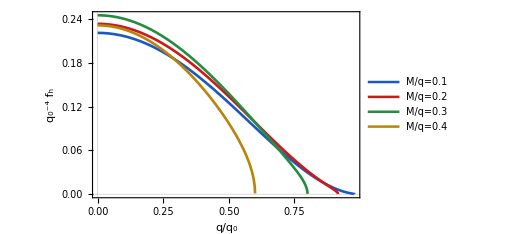

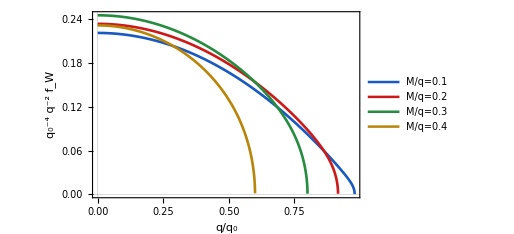

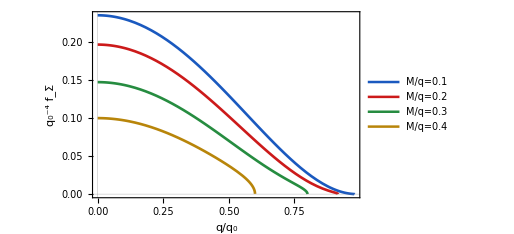

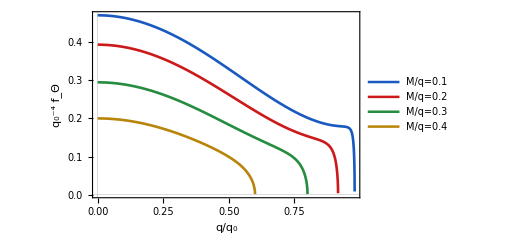

```mathematica
xvalues=Range[0.1,0.4,0.1]; (* 0< x <1/2*)

thesisColors={RGBColor[0.10,0.35,0.75],(*Blu Classico*)
RGBColor[0.80,0.10,0.10],(*Rosso*)
RGBColor[0.15,0.55,0.25],(*Verde Foresta*)
RGBColor[0.72,0.52,0.04],(*Giallo Scuro/Oro*)
RGBColor[0.45,0.15,0.55]  (*Viola/Indaco per il 5° valore*)
};

scientificPlotOptions[yLabel_,pos_]:=Sequence[PlotTheme->"Scientific",Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{Superscript[Subscript[Style["q",Italic],Style["0",Italic]],Style["-4",Italic]],yLabel}],TraditionalForm]],FontSize->16]},PlotLabel->None,BaseStyle->{FontFamily->"Times",FontSize->11},ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[1]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[2]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[3]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[4]]}],TraditionalForm]],FontSize->11]},LegendFunction->"Frame"],pos]];

scientificPlotOptions2[yLabel_]:=Sequence[PlotTheme->"Scientific",Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{Superscript[Subscript[Style["q",Italic],Style["0",Italic]],Style["-4",Italic]],Superscript[Style["q",Italic],Style["-2",Italic]],yLabel}],TraditionalForm]],FontSize->16]},PlotLabel->None,BaseStyle->{FontFamily->"Times",FontSize->11},ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[1]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[2]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[3]]}],TraditionalForm]],FontSize->11],Style[DisplayForm[FormBox[RowBox[{"M","/","q","=",xvalues[[4]]}],TraditionalForm]],FontSize->11]},LegendFunction->"Frame"],{0.25,0.35}]];

plotTensor=Plot[Evaluate@Table[ConditionalExpression[Funzhnew[x,y],y<=Sqrt[1-4 x^2]],{x,xvalues}],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["h",Italic]],{0.84,0.74}]];
Print[plotTensor];

plotVector=Plot[Evaluate[Table[ConditionalExpression[FunzWnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions2[Subscript[Style["f",Italic],Style["W",Italic]]]];Print[plotVector];

plotSigma=Plot[Evaluate[Table[ConditionalExpression[FunzΣnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Σ",Italic]],{0.84,0.74}]];
Print[plotSigma];

 plotTheta=Plot[Evaluate[Table[ConditionalExpression[FunzΘnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Θ",Italic]],{0.84,0.74}]];Print[plotTheta]
```